```mathematica
treeR[n_]:=Table[o[trees[a],trees[n-a]],{a,1,n-1}]
treeR[1]:=n
tree[n_]:=Flatten[treeR[n]//.{o[a_List,b_]:>(o[#,b]&/@a),o[a_,b_List]:>(o[a,#]&/@b)}]
game24play[val_List]:=Union[StringReplace[StringTake[ToString[#,InputForm],{10,-2}],"-1*"~~n_:>"-"<>n]&/@(HoldForm/@Select[Union@Flatten[Outer[#/.{o[q_Integer]:>#2[[q]],n[q_]:>#3[[q]]}&,Block[{O=1,N=1},#/.{o:>o[O++],n:>n[N++]}]&/@tree[4],Tuples[{Plus,Subtract,Times,Divide},3],Permutations[Array[v,4]],1]],Quiet[(#/.v[q_]:>val[[q]])==24]&]/.Table[v[q]->val[[q]],{q,4}])]
```

```mathematica
game24play[RandomInteger[{1,9},4]]
```

{}

```mathematica
Hyperlink[Poker24,"https://rosettacode.org/wiki/24_game/Solve#Mathematica_.2F_Wolfram_Language"]
```

[Poker24](https://rosettacode.org/wiki/24_game/Solve#Mathematica_.2F_Wolfram_Language)

```mathematica
16^6
```

16777216

```mathematica
FindMinimumCostFlow
```

```mathematica
N[Log10[Pi^Pi^Pi^Pi],20]
```

6.6626245297084850396×10^17

```mathematica
IntegerPart[6.662624529708485039580964883850909663`20.*^17]
```

666262452970848503

```mathematica
Log10[666 262 452 970 848 503]
```

Log[32632438400709120]/Log[10]

```mathematica
IntegerPart[Log[32632438400709120]/Log[10]]
```

16

```mathematica
E//N
```

2.71828

```mathematica
E//N
```

2.71828

```mathematica
<<Deus`
```

{{{8,15,19},{24,1,17},{10,26,6}},{{12,25,5},{7,14,21},{23,3,16}},{{22,2,18},{11,27,4},{9,13,20}}}

```mathematica
$Context
```

BTools`Private`

```mathematica
Clear[v]
```

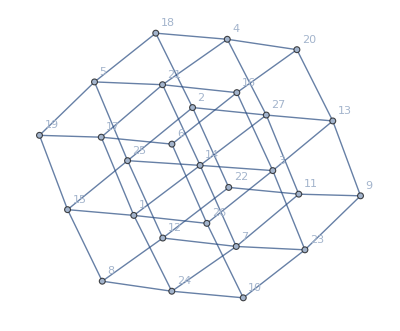

SetDelayed::write: … 中的标签 Function 被保护.

$Failed

```mathematica
g=GridGraph[{3,3,3},VertexLabels->Table[i->Flatten[Magic[3,3]][[i]],{i,3^3}]]
f[v_]:=Graph3D[g,PlotTheme->"LargeGraph",ViewPoint->v,SphericalRegion->True]
```

```mathematica
gifs=Table[v[{Sin[t],Cos[t],0.5}],{t,0,2Pi}]
ListAnimate@gifs
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}